## Formmulae come first

```mathematica
MyGatherBy[items_,crit_]:=Block[{result={},i, found,current=0},
Monitor[
Table[
current++;
found=False;
For[i=1,i≤ Length[result],i++,
If[crit[item,result[[i,1]]],
result[[i]]=Append[result[[i]],item];
found=True;
i=Length[item]+1
];
];
If[!found,AppendTo[result,{item}]]
,{item, items}
],
{item,current,Length[items],Length[result]}];
result
]
```

```mathematica
MyGatherBy2[items_,g_]:=Block[{result={},i, found,current=0,g1,g2,edge},
Monitor[
Table[
current++;
found=False;
g1=VertexContract[g,{item[[1]],item[[2]]}];
For[i=1,i≤ Length[result],i++,
edge=First[result[[i]]];
g2=VertexContract[g,{edge[[1]],edge[[2]]}];
If[IsomorphicGraphQ[g1,g2]  ,
result[[i]]=Append[result[[i]],item];
found=True;
i=Length[result]+1
];
];
If[!found,AppendTo[result,{item}]]
,{item, items}
],
{item,current,Length[items],Length[result],{item,First[result[[i]]]}}];
result
]
```

```mathematica
FormatZero[n_]:=If[n=={},Style[n,Red,Bold],n]
```

```mathematica
MatchPairs[with_,contract_]:=Block[{vertices=Join[with,contract],ws1,cs1,edges={}},
Table[
ws1=SymbolToSets[w1];
Table[
cs1=SymbolToSets[c1];
If[PartitionHasPattern[ws1,cs1],
AppendTo[edges,w1->c1];
Goto[done]
];
,
{c1,contract}
],
{w1,with}
];
Label[done];
edges
]
```

```mathematica
MpgChainMat2[g_]:=Block[{mpgs,groups, formula},
mpgs=Map[SortEdge,CollectMPGEdges[g]];
groups=MyGatherBy2[mpgs,g];
formula=FindFullFormula4[g];
Flatten[
Table[
Table[
With[{p=MatchPairs[formula, FindFullFormula4[EdgeContract[g,edge[[2]]<->edge[[1]]]]] },
{edge,FormatZero[p]}
]
,{edge,Take[bucket,1]}]
,{bucket,groups}
],1]
]
```

```mathematica
Monitor[Table[Print[k<->MpgChainMat2[Graph[plantri[[k]]]]],{k,10}],k]
```

1<->{{1<->2,2},{1<->3,2},{1<->4,2},{1<->5,2},{1<->6,2},{2<->6,2},{2<->7,2},{2<->8,2},{2<->3,2},{3<->8,2},{3<->9,2},{3<->4,2},{4<->9,2},{4<->10,2},{4<->5,2},{5<->10,2},{5<->11,2},{5<->6,2},{6<->11,2},{6<->7,2},{7<->11,2},{7<->12,2},{7<->8,2},{8<->12,2},{8<->9,2},{9<->12,2},{9<->10,2},{10<->12,2},{10<->11,2},{11<->12,2}}

2<->{{1<->2,2},{1<->3,2},{1<->4,2},{1<->5,2},{1<->6,2},{1<->7,2},{8<->14,2},{9<->14,2},{10<->14,2},{11<->14,2},{12<->14,2},{13<->14,2},{2<->7,3},{2<->3,3},{3<->4,3},{4<->5,3},{5<->6,3},{6<->7,3},{8<->13,3},{8<->9,3},{9<->10,3},{10<->11,3},{11<->12,3},{12<->13,3},{2<->8,6},{2<->9,6},{3<->9,6},{3<->10,6},{4<->10,6},{4<->11,6},{5<->11,6},{5<->12,6},{6<->12,6},{6<->13,6},{7<->13,6},{7<->8,6}}

```mathematica
Monitor[Table[Print[k<->MpgChainMat2[Graph[plantri[[k]]]]],{k,10}],k]
```

$Aborted

```mathematica
GroupBy[{{1<->2,0},{1<->3,0},{1<->4,2},{1<->5,2},{1<->6,2},{2<->6,2},{2<->7,2},{2<->8,2},{2<->3,0},{3<->8,2},{3<->9,2},{3<->4,2},{4<->9,2},{4<->10,2},{4<->5,2},{5<->10,2},{5<->11,2},{5<->6,2},{6<->11,2},{6<->7,2},{7<->11,2},{7<->12,2},{7<->8,2},{8<->12,2},{8<->9,2},{9<->12,2},{9<->10,2},{10<->12,2},{10<->11,2},{11<->12,2}},#[[2]]&]
```

<|0→{{1<->2,0},{1<->3,0},{2<->3,0}},2→{{1<->4,2},{1<->5,2},{1<->6,2},{2<->6,2},{2<->7,2},{2<->8,2},{3<->8,2},{3<->9,2},{3<->4,2},{4<->9,2},{4<->10,2},{4<->5,2},{5<->10,2},{5<->11,2},{5<->6,2},{6<->11,2},{6<->7,2},{7<->11,2},{7<->12,2},{7<->8,2},{8<->12,2},{8<->9,2},{9<->12,2},{9<->10,2},{10<->12,2},{10<->11,2},{11<->12,2}}|>

```mathematica
MpgChainMat2[Graph[plantri[[3]]]]
```

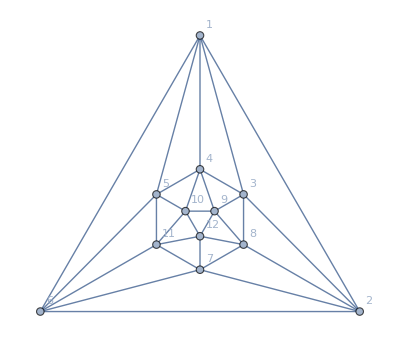

```mathematica
Graph[plantri[[1]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

## Experiments come later

```mathematica
EdgeList[Graph[plantri[[2]]]]//Length
```

36

```mathematica
With[{g=Graph[plantri[[1]]]},MyGatherBy2[CollectMPGEdges[g],g]]
```

{{1<->2,1<->3,1<->4,1<->5,1<->6,2<->6,2<->7,2<->8,2<->3,3<->8,3<->9,3<->4,4<->9,4<->10,4<->5,5<->10,5<->11,5<->6,6<->11,6<->7,7<->11,7<->12,7<->8,8<->12,8<->9,9<->12,9<->10,10<->12,10<->11,11<->12}}

```mathematica
With[{g=Graph[plantri[[2]]]},MyGatherBy2[CollectMPGEdges[g],g]]
```

{{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,8<->14,9<->14,10<->14,11<->14,12<->14,13<->14},{2<->7,2<->3,3<->4,4<->5,5<->6,6<->7,8<->13,8<->9,9<->10,10<->11,11<->12,12<->13},{2<->8,2<->9,3<->9,3<->10,4<->10,4<->11,5<->11,5<->12,6<->12,6<->13,7<->13,7<->8}}

```mathematica
{2<->3,2<->9}
```

```mathematica
With[{g=Graph[plantri[[3]]]},MyGatherBy2[CollectMPGEdges[g],g]]
```

{{1<->2,1<->4,1<->5,1<->7,2<->8,4<->11,5<->11,7<->8,8<->14,8<->15,11<->15,11<->14},{1<->3,1<->6,8<->13,8<->9,10<->11,11<->12},{2<->7,4<->5,14<->15},{2<->9,2<->3,3<->4,4<->10,5<->12,5<->6,6<->7,7<->13,9<->15,10<->15,12<->14,13<->14},{3<->9,3<->10,6<->12,6<->13,9<->10,12<->13}}

```mathematica
With[{g=Graph[plantri[[3]]]},With[{g1=EdgeContract[g,2<->3],g2=EdgeContract[g,2<->9]},
IsomorphicGraphQ[g1,g2]]
]
```

True

```mathematica
MpgChainMat2[Graph[plantri[[2]]]]
```

{{1<->2,{v1ex25adx368bx479c→v1ex368bx479cx5ad}},{2<->7,{v1adx25ex368bx479c→v1adx25ex368bx49c}},{2<->8,{v19bdx2acx357ex468→v19bdx2acx357ex46}}}

```mathematica
MpgChainMat2[Graph[plantri[[3]]]]
```

{{1<->2,{v1dfx25aex368bx479c→v1dfx368bx479cx5ae}},{1<->3,{v1dfx25aex368bx479c→v1dfx25aex479cx68b}},{2<->7,{v1dfx25aex368bx479c→v1dfx25aex368bx49c}},{2<->9,{v19bdx246ex37cfx58a→v1bdx246ex37cfx58a}},{3<->9,{v19bdx246fx357ex8ac→v1bdx246fx357ex8ac}}}

```mathematica
Table[MpgChainMat2[ReadGrof[k]],{k,1,3}]
```

```mathematica
Map[Length,%558,{2}]//Length
```

35

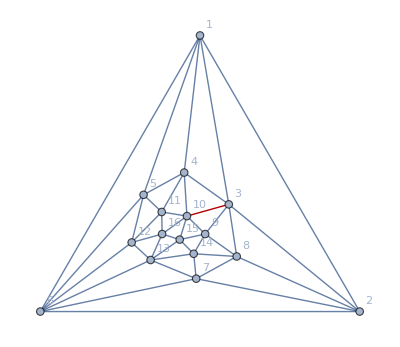

```mathematica
With[{g=plantri[[5]]},
Graph[g,GraphHighlight->{3<->10}, GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
]
```

```mathematica
With[{g=plantri[[5]]},
MyGatherBy2[CollectMPGEdges[g],g]
]
```

{{1<->2,15<->16},{1<->3,2<->6,10<->15,13<->16},{1<->4,2<->7,9<->15,12<->16},{1<->5,2<->8,11<->16,14<->15},{1<->6,2<->3,10<->16,13<->15},{3<->8,5<->6,10<->11,13<->14},{3<->9,4<->10,6<->12,7<->13},{3<->10,6<->13},{3<->4,6<->7,9<->10,12<->13},{4<->11,5<->12,7<->14,8<->9},{4<->5,7<->8,9<->14,11<->12},{5<->11,8<->14}}

```mathematica
MyPrint[f_]:=(Print[f, Length[f]];f)
```

```mathematica
Length[CollectMPGEdges[Graph[plantri⟦5⟧]]]
```

42

```mathematica
Block[{mpgs,groups,formula,g=Graph[plantri⟦5⟧]},mpgs=SortEdge/@CollectMPGEdges[g];groups=MyGatherBy2[mpgs,g];formula=FindFullFormula4[g];Print[formula, Length[formula]];Table[With[{p=MatchPairs[formula,MyPrint[FindFullFormula4[EdgeContract[g,edge⟦1⟧<->edge⟦2⟧]]]]},{edge,FormatZero[p]}],{edge,{3<->10,6<->13}}]]
```

{v1acex29bdx357gx468f,v1acex29bdx357fx468g,v1acex259dx37bfx468g,v1acex249dx357gx68bf,v19bdx2acex357gx468f,v19bdx2acex357fx468g,v19bdx25aex37cfx468g,v18bdx2acex357fx469g,v18acx29bdx357fx46eg,v18bdx25aex37cfx469g,v18acx259dx37bfx46eg,v18cfx25adx36bex479g,v18adx259gx36bex47cf,v18bfx25adx36egx479c,v18adx25egx36bfx479c,v18adx24cex36bfx579g,v18adx24cfx36bex579g,v17acx29bdx35egx468f,v179gx25adx36bex48cf,v179bx25adx36egx48cf,v179gx24cex36bfx58ad,v17cfx249gx36bex58ad,v179gx24cfx36bex58ad,v17bfx249cx36egx58ad,v179cx24egx36bfx58ad,v179bx24cfx36egx58ad,v17acx249dx35egx68bf}27

{v19bdx25egx37cx468f,v18cfx29bdx357x46eg,v18bdx259gx36ex47cf,v18bfx259dx37cx46eg,v18bdx24cfx36ex579g,v17cfx29bdx35ex468g,v17bfx259dx3cex468g,v179gx24cex35dx68bf,v179cx24egx35dx68bf}9

{v1acex259gx37bfx468,v1acex249gx357fx68b,v18bfx2acex357gx469,v18cfx25aex36bx479g,v18acx25egx37bfx469,v18acx24egx357fx69b,v179gx25aex36bx48cf,v17bfx249cx35egx68a,v179bx24cfx35egx68a}9

{{3<->10,{}},{6<->13,{}}}

```mathematica
Block[{mpgs,groups, formula,g=plantri[[5]]},
mpgs=Map[SortEdge,CollectMPGEdges[g]];
groups=MyGatherBy2[mpgs,g];
formula=FindFullFormula4[g];
Print[formula];
Table[
With[{p=FindFullFormula4[EdgeContract[g,edge[[1]]<->edge[[2]]]] },
{edge,p}
]
,{edge,{3<->10,6<->13}}]
]
```

{v1acex29bdx357gx468f,v1acex29bdx357fx468g,v1acex259dx37bfx468g,v1acex249dx357gx68bf,v19bdx2acex357gx468f,v19bdx2acex357fx468g,v19bdx25aex37cfx468g,v18bdx2acex357fx469g,v18acx29bdx357fx46eg,v18bdx25aex37cfx469g,v18acx259dx37bfx46eg,v18cfx25adx36bex479g,v18adx259gx36bex47cf,v18bfx25adx36egx479c,v18adx25egx36bfx479c,v18adx24cex36bfx579g,v18adx24cfx36bex579g,v17acx29bdx35egx468f,v179gx25adx36bex48cf,v179bx25adx36egx48cf,v179gx24cex36bfx58ad,v17cfx249gx36bex58ad,v179gx24cfx36bex58ad,v17bfx249cx36egx58ad,v179cx24egx36bfx58ad,v179bx24cfx36egx58ad,v17acx249dx35egx68bf}

{{3<->10,{v19bdx25egx37cx468f,v18cfx29bdx357x46eg,v18bdx259gx36ex47cf,v18bfx259dx37cx46eg,v18bdx24cfx36ex579g,v17cfx29bdx35ex468g,v17bfx259dx3cex468g,v179gx24cex35dx68bf,v179cx24egx35dx68bf}},{6<->13,{v1acex259gx37bfx468,v1acex249gx357fx68b,v18bfx2acex357gx469,v18cfx25aex36bx479g,v18acx25egx37bfx469,v18acx24egx357fx69b,v179gx25aex36bx48cf,v17bfx249cx35egx68a,v179bx24cfx35egx68a}}}

```mathematica
Monitor[Table[k<->Framed[Column[MpgChainMat2[Graph[plantri[[k]]]]]],{k,1,15}],{"plantri",k}]//TableForm
```

1<->{1<->2,{v19bx25cx37ax468→v19bx37ax468x5c}}
2<->{1<->2,{v1ex25adx368bx479c→v1ex368bx479cx5ad}}
{2<->7,{v1adx25ex368bx479c→v1adx25ex368bx49c}}
{2<->8,{v19bdx2acx357ex468→v19bdx2acx357ex46}}
3<->{1<->2,{v1dfx25aex368bx479c→v1dfx368bx479cx5ae}}
{1<->3,{v1dfx25aex368bx479c→v1dfx25aex479cx68b}}
{2<->7,{v1dfx25aex368bx479c→v1dfx25aex368bx49c}}
{2<->9,{v19bdx246ex37cfx58a→v1bdx246ex37cfx58a}}
{3<->9,{v19bdx246fx357ex8ac→v1bdx246fx357ex8ac}}
4<->{1<->2,{v1acex29bdx357gx468f→v1acex357gx468fx9bd}}
{1<->3,{v17cfx249gx36bex58ad→v17cfx249gx58adx6be}}
{1<->4,{v18cfx25adx36bex479g→v18cfx25adx36bex79g}}
5<->{1<->2,{v1acex29bdx357gx468f→v1acex357gx468fx9bd}}
{1<->3,{v17cfx249gx36bex58ad→v17cfx249gx58adx6be}}
{1<->4,{v18cfx25adx36bex479g→v18cfx25adx36bex79g}}
{1<->5,{v18adx259gx36bex47cf→v18adx29gx36bex47cf}}
{1<->6,{v18bfx25adx36egx479c→v18bfx25adx3egx479c}}
{3<->8,{v18adx25egx36bfx479c→v1adx25egx36bfx479c}}
{3<->9,{v1acex29bdx357gx468f→v1acex2bdx357gx468f}}
{3<->10,{}}
{3<->4,{v19bdx25aex37cfx468g→v19bdx25aex37cfx68g}}
{4<->11,{v1acex29bdx357gx468f→v1acex29dx357gx468f}}
{4<->5,{v1acex249dx357gx68bf→v1acex249dx37gx68bf}}
{5<->11,{v1acex29bdx357fx468g→v1acex29dx357fx468g}}
6<->{1<->2,{v1bdfx25egx379cx468a→v1bdfx379cx468ax5eg}}
{1<->3,{v18dgx25bex379cx46af→v18dgx25bex46afx79c}}
{1<->4,{v1adfx25bex379cx468g→v1adfx25bex379cx68g}}
7<->{1<->2,{v1bdfx29cex357ahx468g→v1bdfx357ahx468gx9ce}}
{1<->3,{v1bdfx29cex357ahx468g→v1bdfx29cex468gx57ah}}
{1<->4,{v18cgx24dfx357ahx69be→v18cgx2dfx357ahx69be}}
{1<->5,{v18ahx259dgx36bex47cf→v18ahx29dgx36bex47cf}}
{1<->6,{v18ahx259dgx36bex47cf→v18ahx259dgx3bex47cf}}
{3<->8,{}}
{3<->9,{v18ahx259dgx36bex47cf→v18ahx25dgx36bex47cf}}
{4<->9,{v18adx24cgx357fhx69be→v18adx24cgx357fhx6be}}
{4<->10,{v1acex259dgx37bfx468h→v1cex259dgx37bfx468h}}
{4<->11,{v18cgx24dfx357ahx69be→v18cgx24dfx357ahx69e}}
{4<->5,{v18acx259dgx36bex47fh→v18acx29dgx36bex47fh}}
{5<->6,{v179cgx2bdfx35aex468h→v179cgx2bdfx35aex48h}}
{10<->15,{v1bdfx29cex357ahx468g→v1bdx29cex357ahx468g}}
8<->{1<->2,{v1acfx29bdx357hx468eg→v1acfx357hx468egx9bd}}
{1<->3,{v17cgx249dhx36bfx58ae→v17cgx249dhx58aex6bf}}
{1<->4,{v19dhx2acfx357bx468eg→v19dhx2acfx357bx68eg}}
{1<->5,{v18bex249dhx357gx6acf→v18bex249dhx37gx6acf}}
{1<->6,{v1acfx29bdx357hx468eg→v1acfx29bdx357hx48eg}}
{2<->6,{v19bdx2acfx357hx468eg→v19bdx2acfx357hx48eg}}
{2<->7,{v17acx259hx3bdfx468eg→v1acx259hx3bdfx468eg}}
{2<->8,{v18adhx24egx36cfx579b→v1adhx24egx36cfx579b}}
{2<->3,{v18adhx25bfx37cgx469e→v18adhx25bfx469ex7cg}}
{3<->8,{}}
{3<->4,{}}
{6<->7,{}}
{7<->14,{v1acfx29dhx357bx468eg→v1acfx29dhx357bx468g}}
{7<->15,{v1acfx29dhx357bx468eg→v1acx29dhx357bx468eg}}
9<->{1<->2,{v1cegx25adfx368bx479h→v1cegx368bx479hx5adf}}
{1<->3,{v1cegx25adfx368bx479h→v1cegx25adfx479hx68b}}
{1<->4,{v1cegx25adfx368bx479h→v1cegx25adfx368bx79h}}
{1<->5,{v1adfx24cegx368bx579h→v1adfx24cegx368bx79h}}
{1<->6,{v19bex25adfx37cgx468h→v19bex25adfx37cgx48h}}
{1<->7,{v1acfx246egx38bdx579h→v1acfx246egx38bdx59h}}
{2<->7,{v18bdx2acfx357ghx469e→v18bdx2acfx35ghx469e}}
{2<->9,{v18adx26bex357ghx49cf→v18adx26bex357ghx4cf}}
{3<->9,{v19bex246ghx37cfx58ad→v1bex246ghx37cfx58ad}}
{3<->10,{v19bex25adfx368hx47cg→v19bex25dfx368hx47cg}}
{3<->4,{v19bex25adfx37cgx468h→v19bex25adfx37cgx68h}}
{4<->10,{v19bex25adfx37cgx468h→v19bex25dfx37cgx468h}}
{4<->11,{v18bdx2acfx357ghx469e→v18dx2acfx357ghx469e}}
{4<->5,{v1cegx25adfx368bx479h→v1cegx2adfx368bx479h}}
{5<->11,{v19bex246ghx358dx7acf→v19ex246ghx358dx7acf}}
{5<->12,{v1acex246ghx38bdx579f→v1aex246ghx38bdx579f}}
{5<->6,{v19bdx246egx37cfx58ah→v19bdx24egx37cfx58ah}}
{6<->12,{v1acfx246egx38bdx579h→v1afx246egx38bdx579h}}
{6<->13,{v1cegx25adfx368bx479h→v1cegx25afx368bx479h}}
{7<->13,{v1acex246ghx38bdx579f→v1acex246ghx38bx579f}}
{10<->11,{v18bdx26aex357ghx49cf→v18dx26aex357ghx49cf}}
{11<->17,{v1cegx25adfx368bx479h→v1cegx25adfx368bx479}}
{12<->17,{v19bex25adfx37cgx468h→v19bex25adfx37cgx468}}
{12<->13,{v1acfx246egx38bdx579h→v1acfx246egx38bx579h}}
10<->{1<->2,{v1egx25adfx368bhx479c→v1egx368bhx479cx5adf}}
{1<->3,{v1egx25adfx368bhx479c→v1egx25adfx479cx68bh}}
{1<->4,{v1egx25adfx368bhx479c→v1egx25adfx368bhx79c}}
{2<->6,{v17acfx2bex358dgx469h→v17acfx2bex358dgx49h}}
11<->{1<->2,{v1egx259dhx37acfx468bi→v1egx37acfx468bix59dh}}
{1<->3,{v1egx259dhx37acfx468bi→v1egx259dhx468bix7acf}}
{1<->5,{v1egx259dhx37acfx468bi→v1egx29dhx37acfx468bi}}
{2<->6,{v17acfx29bex35dhx468gi→v17acfx29bex35dhx48gi}}
{2<->7,{v18adhx24cfx357gix69be→v18adhx24cfx35gix69be}}
{5<->12,{v19dhx25egx37acfx468bi→v19dhx25egx37afx468bi}}
12<->{1<->2,{v1cegx24adfx368hx579bi→v1cegx368hx4adfx579bi}}
{1<->3,{v1cegx24adfx368hx579bi→v1cegx24adfx579bix68h}}
{1<->4,{v19ehx24adfx368cix57bg→v19ehx2adfx368cix57bg}}
{1<->5,{v179bix2cegx358hx46adf→v179bix2cegx38hx46adf}}
{1<->6,{v19bdfx2cegx357hx468ai→v19bdfx2cegx357hx48ai}}
{2<->7,{v18acex2bdgx357ix469fh→v18acex2bdgx35ix469fh}}
{2<->8,{v19bdfx24ehx357gx68aci→v19bdfx24ehx357gx6aci}}
{2<->3,{v19bdfx2cegx357hx468ai→v19bdfx2cegx468aix57h}}
{4<->11,{v19bdfx24egx357hx68aci→v19dfx24egx357hx68aci}}
13<->{1<->2,{v1cegx29bfx357aix468dh→v1cegx357aix468dhx9bf}}
{1<->3,{v1cegx29bfx357aix468dh→v1cegx29bfx468dhx57ai}}
{1<->4,{v1cegx29bfx357aix468dh→v1cegx29bfx357aix68dh}}
{1<->5,{v19fhx24cegx357aix68bd→v19fhx24cegx37aix68bd}}
{1<->6,{v1acfx29beix357gx468dh→v1acfx29beix357gx48dh}}
{2<->6,{v1cegx29bfx357aix468dh→v1cegx29bfx357aix48dh}}
{2<->7,{v18acex259ix37bdgx46fh→v18acex259ix3bdgx46fh}}
{2<->8,{}}
{2<->3,{v19bfx2cegx357aix468dh→v19bfx2cegx468dhx57ai}}
{3<->8,{v18aeix259fhx36bdx47cg→v1aeix259fhx36bdx47cg}}
{3<->9,{v18aeix259fhx37bdx46cg→v18aeix25fhx37bdx46cg}}
{3<->4,{v19beix25afx37cgx468dh→v19beix25afx37cgx68dh}}
{4<->9,{v18acex259ix37bdgx46fh→v18acex25ix37bdgx46fh}}
{4<->5,{v18acex259fhx36bdgx47i→v18acex29fhx36bdgx47i}}
{5<->12,{v1acfx29beix357gx468dh→v1afx29beix357gx468dh}}
{5<->13,{v1acfx29beix357gx468dh→v1acfx29beix357gx468h}}
{6<->14,{v1acex259fhx37bdgx468i→v1acx259fhx37bdgx468i}}
{6<->7,{v18aeix259fhx37bdgx46c→v18aeix259fhx3bdgx46c}}
{7<->14,{v19beix25afx37cgx468dh→v19bix25afx37cgx468dh}}
{7<->15,{v18beix259fhx37acx46dg→v18beix259hx37acx46dg}}
{7<->8,{v18aeix259fhx36bdgx47c→v1aeix259fhx36bdgx47c}}
{8<->15,{v1aeix259fhx37bdgx468c→v1aeix259hx37bdgx468c}}
{8<->16,{v1aeix259fhx37bdgx468c→v1aeix259fhx37bdx468c}}
{8<->9,{v19bfx24cegx357aix68dh→v1bfx24cegx357aix68dh}}
{13<->15,{v18aeix259fhx36bdx47cg→v18aeix259hx36bdx47cg}}
{13<->14,{v18beix24dgx36acfx579h→v18bix24dgx36acfx579h}}
14<->{1<->2,{v1cegx25afhx368bdx479i→v1cegx368bdx479ix5afh}}
{1<->3,{v1cegx25afhx368bdx479i→v1cegx25afhx479ix68bd}}
{1<->4,{v17dgx2acex358bix469fh→v17dgx2acex358bix69fh}}
{1<->5,{v18ahx2cegx357bix469df→v18ahx2cegx37bix469df}}
{2<->7,{v18acex2dgx357bix469fh→v18acex2dgx35bix469fh}}
{2<->8,{v19bdfx24ehx357gx68aci→v19bdfx24ehx357gx6aci}}
{3<->9,{v19bdfx24egx357hx68aci→v1bdfx24egx357hx68aci}}
{3<->10,{v19bex25afhx368cix47dg→v19bex25fhx368cix47dg}}
{3<->4,{v18acex25bix37dgx469fh→v18acex25bix37dgx69fh}}
{4<->10,{v19bdfx24ehx357gx68aci→v19bdfx24ehx357gx68ci}}
{4<->11,{v1cegx25afhx368bdx479i→v1cegx25afhx368dx479i}}
{4<->12,{v1cegx25afhx368bdx479i→v1egx25afhx368bdx479i}}
{4<->5,{v1cegx25afhx368bdx479i→v1cegx2afhx368bdx479i}}
{8<->15,{v1cegx25afhx368bdx479i→v1cegx25ahx368bdx479i}}
{8<->16,{v179bix25afhx3cegx468d→v179bix25afhx3cex468d}}
{8<->9,{v179bdx25afhx3cegx468i→v17bdx25afhx3cegx468i}}
{10<->16,{v17adx2cegx358bix469fh→v17adx2cex358bix469fh}}
{10<->11,{v18adx2cegx357bix469fh→v18adx2cegx357ix469fh}}
{11<->16,{}}
{11<->17,{v19bex25afhx368cix47dg→v19bex25afx368cix47dg}}
{11<->12,{v1cegx25afhx368bix479d→v1egx25afhx368bix479d}}
{12<->17,{v19cex25afhx368bix47dg→v19cex25afx368bix47dg}}
{12<->13,{v18aehx2cgx357bix469df→v18aehx2cgx357bix469f}}
{16<->17,{v19bdfx24egx368cix57ah→v19bdfx24egx368cix57a}}
15<->{1<->2,{v1bdfx29cegx357ahx468i→v1bdfx357ahx468ix9ceg}}
{1<->3,{v1bdfx29cegx357ahx468i→v1bdfx29cegx468ix57ah}}
{1<->4,{v18dgx259bex37acix46fh→v18dgx259bex37acix6fh}}
{1<->5,{v19bex24dgx357fhx68aci→v19bex24dgx37fhx68aci}}
{1<->6,{v19cegx2bdfx357ahx468i→v19cegx2bdfx357ahx48i}}
{2<->7,{v18adx259bix36cegx47fh→v18adx259bix36cegx4fh}}
{2<->8,{v19bex24dgx357fhx68aci→v19bex24dgx357fhx6aci}}
{3<->8,{v18bdx259egx36acix47fh→v1bdx259egx36acix47fh}}
{3<->9,{v19cegx24dfx357bix68ah→v1cegx24dfx357bix68ah}}
{3<->4,{v17acix259bex36fhx48dg→v17acix259bex36fhx8dg}}
{4<->9,{v19bex24dgx357fhx68aci→v1bex24dgx357fhx68aci}}
{4<->12,{v1bdfx29cegx357ahx468i→v1bdfx29egx357ahx468i}}
{5<->12,{v1bdfx29cegx357aix468h→v1bdfx29egx357aix468h}}
{8<->14,{v1bdfx29cegx357aix468h→v1bdfx29cgx357aix468h}}
{8<->15,{v1bdfx29cegx357aix468h→v1bdx29cegx357aix468h}}

```mathematica
Monitor[Table[k<->Framed[Column[MpgChainMat2[Graph[plantri[[k]]]]]],{k,16,25}],{"plantri",k}]//TableForm
```

16<->{1<->2,{v1dfhx259bex37cgx468ai→v1dfhx37cgx468aix59be}}
{1<->3,{v1dfhx259bex37cgx468ai→v1dfhx259bex468aix7cg}}
{1<->4,{v1dfhx259bex37cgx468ai→v1dfhx259bex37cgx68ai}}
{1<->5,{v19bex24adfx357gix68ch→v19bex24adfx37gix68ch}}
{1<->6,{v1cfhx259bex37dgx468ai→v1cfhx259bex37dgx48ai}}
{2<->6,{v17bdgx249ix36cfhx58ae→v17bdgx249ix3cfhx58ae}}
{2<->7,{v18acex29bdx357gix46fh→v18acex29bdx35gix46fh}}
{2<->8,{v18bdgx25aex36cfhx479i→v1bdgx25aex36cfhx479i}}
{2<->3,{v179bdx25gix36cfhx48ae→v179bdx25gix48aex6cfh}}
{3<->8,{v18bex25afix36cgx479dh→v1bex25afix36cgx479dh}}
{3<->9,{v1adfx259bex37chx468gi→v1adfx25bex37chx468gi}}
{3<->10,{v18acex25bgx36fix479dh→v18cex25bgx36fix479dh}}
{3<->11,{v1cfhx259bex37dgx468ai→v1cfhx259ex37dgx468ai}}
{3<->4,{v1cfhx259bex37dgx468ai→v1cfhx259bex37dgx68ai}}
{4<->11,{v18aix259bex36cfhx47dg→v18aix259ex36cfhx47dg}}
{4<->12,{v18acex2bdfx357gix469h→v18aex2bdfx357gix469h}}
{4<->5,{v18bdgx25aex36cfhx479i→v18bdgx2aex36cfhx479i}}
{5<->12,{v18bdgx29cex357hx46afi→v18bdgx29ex357hx46afi}}
{5<->6,{v179bdx2acex35fhx468gi→v179bdx2acex35fhx48gi}}
{6<->7,{v18acex2bdfx357gix469h→v18acex2bdfx35gix469h}}
{7<->15,{v1adfx259bex37chx468gi→v1adx259bex37chx468gi}}
{7<->8,{v18bdgx259ex36cfhx47ai→v1bdgx259ex36cfhx47ai}}
{8<->15,{v1dfhx259bex37cgx468ai→v1dhx259bex37cgx468ai}}
{8<->9,{v19bex24adfx357gix68ch→v1bex24adfx357gix68ch}}
{9<->15,{v18acex2bdfx357gix469h→v18acex2bdx357gix469h}}
17<->{1<->2,{v1egx26acfx358bix479dh→v1egx358bix479dhx6acf}}
{1<->3,{v1egx26acfx358bix479dh→v1egx26acfx479dhx58bi}}
{1<->4,{v1egx26acfx358bix479dh→v1egx26acfx358bix79dh}}
{1<->5,{v1egx26acfx358bix479dh→v1egx26acfx38bix479dh}}
{1<->6,{v1cgx25aehx368bix479df→v1cgx25aehx38bix479df}}
{1<->7,{v1cgx25aehx368bix479df→v1cgx25aehx368bix49df}}
{2<->7,{v1cegx25ahx368bix479df→v1cegx25ahx368bix49df}}
{2<->8,{v1cegx26ahx358bix479df→v1cegx26ahx35bix479df}}
{2<->9,{v19bdfx24ehx357gix68ac→v1bdfx24ehx357gix68ac}}
{2<->3,{v1aehx26cgx358bix479df→v1aehx26cgx479dfx58bi}}
{3<->9,{v19cex246gix37bdfx58ah→v1cex246gix37bdfx58ah}}
{4<->11,{v1cegx26ahx358bix479df→v1cegx26ahx358ix479df}}
{4<->12,{v18adhx2cegx357bix469f→v18adhx2egx357bix469f}}
{4<->5,{v19bdfx25aehx368cx47gi→v19bdfx2aehx368cx47gi}}
{5<->12,{v1cegx25afx368bix479dh→v1egx25afx368bix479dh}}
{5<->13,{v1cegx25ahx368bix479df→v1cegx25ahx368bix479f}}
{5<->6,{v1egx26acfx358bix479dh→v1egx2acfx358bix479dh}}
{6<->13,{v1cegx26ahx358bix479df→v1cegx26ahx358bix479f}}
{6<->14,{v1cegx26ahx358bix479df→v1cgx26ahx358bix479df}}
{6<->7,{v18adhx2cegx357bfx469i→v18adhx2cegx35bfx469i}}
{7<->14,{v19bdfx25aehx37cgx468i→v19bdfx25ahx37cgx468i}}
{12<->18,{v1cgx25aehx368bix479df→v1cgx25aehx368bx479df}}
{12<->13,{v1cgx25aehx368bix479df→v1cgx25aehx368bix479f}}
18<->{1<->2,{v1dfix2behx3579cgx468a→v1dfix3579cgx468axbeh}}
{1<->3,{v1dfix2behx3579cgx468a→v1dfix2behx468ax579cg}}
{1<->5,{v1bfhx26dix3579cgx48ae→v1bfhx26dix379cgx48ae}}
{1<->6,{v1acgx25bfhx368dix479e→v1acgx25bfhx38dix479e}}
{3<->10,{v19bdfx26gix358cx47aeh→v19bdfx26gix358cx47eh}}
{6<->14,{v1dfix2behx3579cgx468a→v1dfix2bhx3579cgx468a}}
19<->{1<->2,{v1hix26acfx358bex479dg→v1hix358bex479dgx6acf}}
{1<->3,{v1hix26acfx358bex479dg→v1hix26acfx479dgx58be}}
{1<->4,{v1hix26acfx358bex479dg→v1hix26acfx358bex79dg}}
{2<->7,{v18bex25aix36cfhx479dg→v18bex25aix36cfhx49dg}}
{2<->8,{v1cfhx26aix358bex479dg→v1cfhx26aix35bex479dg}}
{2<->9,{v19bdfx246gx357hix8ace→v1bdfx246gx357hix8ace}}
{2<->3,{v1adgx26cfhx358bex479i→v1adgx26cfhx479ix58be}}
{3<->9,{v19bdfx246hix357gx8ace→v1bdfx246hix357gx8ace}}
{3<->10,{v1adgx246fhx38cex579bi→v1dgx246fhx38cex579bi}}
{3<->4,{v18acex25bix36fhx479dg→v18acex25bix36fhx79dg}}
{4<->10,{v19bdfx25aegx37chx468i→v19bdfx25egx37chx468i}}
{4<->12,{v1adgx246fhx38cex579bi→v1adgx246fhx38ex579bi}}
{9<->10,{v1acex24dfhx368bix579g→v1cex24dfhx368bix579g}}
20<->{1<->2,{v1gix26acfx358bex479dh→v1gix358bex479dhx6acf}}
{1<->3,{v1gix26acfx358bex479dh→v1gix26acfx479dhx58be}}
{1<->4,{v1gix26acfx358bex479dh→v1gix26acfx358bex79dh}}
{1<->5,{v1gix26acfx358bex479dh→v1gix26acfx38bex479dh}}
{1<->6,{v1gix26acfx358bex479dh→v1gix2acfx358bex479dh}}
{1<->7,{v1gix26acfx358bex479dh→v1gix26acfx358bex49dh}}
{2<->8,{v19bdfx2acex357gix468h→v19bdfx2acex357gix46h}}
{2<->9,{v19bdfx246ix37cgx58aeh→v1bdfx246ix37cgx58aeh}}
{2<->3,{v1acfx26gix358bex479dh→v1acfx26gix479dhx58be}}
{3<->9,{v19bdfx246gix37cx58aeh→v1bdfx246gix37cx58aeh}}
{3<->10,{v1acfx246gix358ehx79bd→v1cfx246gix358ehx79bd}}
{3<->4,{v18acex25bfx36gix479dh→v18acex25bfx36gix79dh}}
{4<->10,{v19bdfx2acex357gix468h→v19bdfx2cex357gix468h}}
{4<->11,{v19bdfx25aehx37cgx468i→v19dfx25aehx37cgx468i}}
{4<->12,{v18adhx2cegx357bix469f→v18adhx2egx357bix469f}}
{4<->5,{v19bdx26acfx357gix48eh→v19bdx26acfx37gix48eh}}
{5<->12,{v1cegx25afx368bix479dh→v1egx25afx368bix479dh}}
{5<->13,{v1cegx25afx368bix479dh→v1cegx25afx368bix479h}}
{9<->16,{}}
{9<->10,{v1acfx246gix358bex79dh→v1cfx246gix358bex79dh}}
{10<->16,{v19bdfx2acex357gix468h→v19bdfx2acex357ix468h}}
{10<->11,{v1cegx26afx358bix479dh→v1cegx26afx358ix479dh}}
{11<->16,{v19cfx246gix37bdx58aeh→v19cfx246ix37bdx58aeh}}
{11<->17,{v1gix26acfx358bex479dh→v1gix26acfx358bex479d}}
{11<->12,{v19bex26acfx357gix48dh→v19bex26afx357gix48dh}}
21<->{1<->2,{v1egix29bdx357acx468fh→v1egix357acx468fhx9bd}}
{1<->3,{v1egix29bdx357acx468fh→v1egix29bdx468fhx57ac}}
{1<->4,{v1egix29bdx357acx468fh→v1egix29bdx357acx68fh}}
22<->{1<->2,{}}
{1<->3,{v18ehx25bix369cfx47adg→v18ehx25bix47adgx69cf}}
{1<->4,{v1adfx25begx379cix468h→v1adfx25begx379cix68h}}
{1<->5,{v19bfx25ehx368cix47adg→v19bfx2ehx368cix47adg}}
{1<->6,{v19bfx25ehx368cix47adg→v19bfx25ehx38cix47adg}}
{2<->6,{v179bdx24fhx368cix5aeg→v179bdx24fhx38cix5aeg}}
{2<->8,{v19bdfx25ehx37cgx468ai→v19bdfx25ehx37cgx46ai}}
{2<->9,{v1acegx2bdfx3579ix468h→v1acegx2bdfx357ix468h}}
{3<->10,{v19bdfx25ehx37cgx468ai→v19bdfx25ehx37cgx468i}}
{3<->11,{v1acegx2bdfx3579ix468h→v1acegx2dfx3579ix468h}}
{3<->4,{v1acegx24dfx368hx579bi→v1acegx2dfx368hx579bi}}
{4<->5,{v19bdfx25ehx368cix47ag→v19bdfx2ehx368cix47ag}}
{5<->13,{v19bdfx24ehx368cix57ag→v19bfx24ehx368cix57ag}}
{6<->13,{v17acix2bdgx358ehx469f→v17acix2bgx358ehx469f}}
{9<->10,{v18acix25begx36fhx479d→v18cix25begx36fhx479d}}
23<->{1<->2,{v1cehx29bfjx357agx468di→v1cehx357agx468dix9bfj}}
{1<->3,{v1cehx29bfjx357agx468di→v1cehx29bfjx468dix57ag}}
{1<->4,{v1cehx29bfjx357agx468di→v1cehx29bfjx357agx68di}}
{1<->5,{v179gix25afjx36bdhx48ce→v179gix2afjx36bdhx48ce}}
{1<->6,{v1cfhx29bejx357agx468di→v1cfhx29bejx357agx48di}}
{2<->6,{v1cehx29bfjx357agx468di→v1cehx29bfjx357agx48di}}
{2<->7,{v18aejx29bdx357gix46cfh→v18aejx29bdx35gix46cfh}}
{2<->8,{}}
{2<->3,{v19bfjx2cehx357agx468di→v19bfjx2cehx468dix57ag}}
{3<->8,{v18aejx24cfhx36bdx579gi→v1aejx24cfhx36bdx579gi}}
{3<->9,{v19bfjx24cehx357gix68ad→v1bfjx24cehx357gix68ad}}
{3<->4,{v19begx25afjx37chx468di→v19begx25afjx37chx68di}}
{4<->9,{v18aejx259gix37bdhx46cf→v18aejx25gix37bdhx46cf}}
{4<->10,{v1acegx259fix37bdhx468j→v1cegx259fix37bdhx468j}}
{4<->11,{v1acegx259fix37bdhx468j→v1acegx259fix37dhx468j}}
{4<->5,{v18acex259fjx36bdhx47gi→v18acex29fjx36bdhx47gi}}
{5<->11,{v1behx259fjx37acgx468di→v1ehx259fjx37acgx468di}}
{5<->6,{v179bgx2cehx35afjx468di→v179bgx2cehx35afjx48di}}
{8<->16,{v1acegx259fjx37bdhx468i→v1acex259fjx37bdhx468i}}
{8<->17,{v19egix25afjx37bdhx468c→v19egix25afjx37bdx468c}}
{9<->10,{v1bfhx29cegx357ajx468di→v1bfhx29cegx357jx468di}}
{10<->17,{v18bejx259gix37adx46cfh→v18bejx259gix37adx46cf}}
{10<->18,{v1cehx29bfjx357agx468di→v1cehx29bfjx357agx468d}}
{10<->11,{v19bfjx24cehx357gix68ad→v19fjx24cehx357gix68ad}}
{11<->18,{v1cfhx29begx357ajx468di→v1cfhx29begx357ajx468d}}
{11<->12,{v1cfhx29begx357ajx468di→v1fhx29begx357ajx468di}}
{17<->18,{v1acegx29bfjx357hx468di→v1acegx29bfjx357hx468d}}
24<->{1<->2,{v1bdfx259ehx37acjx468gi→v1bdfx37acjx468gix59eh}}
{1<->3,{v1bdfx259ehx37acjx468gi→v1bdfx259ehx468gix7acj}}
{1<->4,{v17cfx29bdjx35aehx468gi→v17cfx29bdjx35aehx68gi}}
{1<->5,{v1aehx29bdjx357fix468cg→v1aehx29bdjx37fix468cg}}
{1<->6,{v1acex29bdjx357fhx468gi→v1acex29bdjx357fhx48gi}}
{2<->6,{v19bdjx2acex357fhx468gi→v19bdjx2acex357fhx48gi}}
{2<->7,{v18adhx29bjx357fix46ceg→v18adhx29bjx35fix46ceg}}
{2<->8,{}}
{2<->3,{v19bdjx2acex357fhx468gi→v19bdjx2acex468gix57fh}}
{3<->8,{v17bfix259ehx3adjx468cg→v17bfix259ehx3adjx46cg}}
{3<->9,{v19bex24dfhx357gix68acj→v1bex24dfhx357gix68acj}}
{3<->4,{v19bdjx25aehx37cfx468gi→v19bdjx25aehx37cfx68gi}}
{4<->9,{v19bdjx24cegx357fhx68ai→v1bdjx24cegx357fhx68ai}}
{4<->10,{v1adhx259egx37bfix468cj→v1dhx259egx37bfix468cj}}
{4<->11,{v18bdjx29cegx357ahx46fi→v18djx29cegx357ahx46fi}}
{4<->5,{v18bdjx259gix36acex47fh→v18bdjx29gix36acex47fh}}
{5<->11,{v1aehx29bdjx357fix468cg→v1aehx29djx357fix468cg}}
{5<->12,{v1adhx259egx37bfix468cj→v1adhx259egx37bfix468j}}
{5<->13,{v18adhx259jx37bfix46ceg→v18ahx259jx37bfix46ceg}}
{5<->6,{v179cjx2bdfx35aehx468gi→v179cjx2bdfx35aehx48gi}}
{6<->13,{v19bdjx24cegx357fix68ah→v19bjx24cegx357fix68ah}}
{6<->7,{v18bdjx29cegx357ahx46fi→v18bdjx29cegx35ahx46fi}}
{7<->13,{v18bdjx259gix36acex47fh→v18bjx259gix36acex47fh}}
{7<->8,{v18adhx259egx36bfix47cj→v1adhx259egx36bfix47cj}}
{8<->9,{v19cegx24dfhx357aix68bj→v1cegx24dfhx357aix68bj}}
{9<->10,{v1bdfx259ehx37acjx468gi→v1bdfx259ehx37cjx468gi}}
25<->{1<->2,{v1bdfx259ehx37acjx468gi→v1bdfx37acjx468gix59eh}}
{1<->4,{v17cfx29bdjx35aehx468gi→v17cfx29bdjx35aehx68gi}}
{1<->5,{v18adhx259egx36bfix47cj→v18adhx29egx36bfix47cj}}
{2<->6,{v17acjx29bex35dfhx468gi→v17acjx29bex35dfhx48gi}}
{2<->7,{v18bdjx259gix36aehx47cf→v18bdjx259gix36aehx4cf}}
{2<->8,{v19cegx25adhx37bfix468j→v19cegx25adhx37bfix46j}}
{2<->3,{v19bdjx2acex357fhx468gi→v19bdjx2acex468gix57fh}}
{4<->9,{v19bdjx24cegx357fhx68ai→v1bdjx24cegx357fhx68ai}}
{4<->10,{v19cegx25adhx37bfix468j→v19cegx25dhx37bfix468j}}
{4<->11,{v19cegx25adhx37bfix468j→v19cegx25adhx37fix468j}}
{4<->5,{v19cegx24dfhx357aix68bj→v19cegx24dfhx37aix68bj}}
{5<->11,{v19bdjx24cegx357fix68ah→v19djx24cegx357fix68ah}}
{7<->13,{v1acex29bdjx357fhx468gi→v1acex29bjx357fhx468gi}}
{7<->14,{v18bdjx29cegx357ahx46fi→v18bdjx29cgx357ahx46fi}}
{7<->8,{v18adhx259egx36bfix47cj→v1adhx259egx36bfix47cj}}
{8<->14,{v19cegx25adjx37bfix468h→v19cgx25adjx37bfix468h}}
{10<->15,{v19cegx25adhx37bfix468j→v19cegx25adhx37bix468j}}
{10<->16,{v1acex29bdjx357fhx468gi→v1acex29bdjx357fhx468i}}
{10<->11,{v19bdjx24cegx357fhx68ai→v19djx24cegx357fhx68ai}}
{11<->16,{v19bex25dfhx37acjx468gi→v19bex25dfhx37acjx468i}}
{11<->17,{v1bdfx259ehx37acjx468gi→v1bdfx259ex37acjx468gi}}
{11<->12,{v19bex25dfhx37acjx468gi→v19bex25dfhx37ajx468gi}}
{14<->18,{v19bex25dfhx37acjx468gi→v19bex25dfhx37acjx468g}}
{14<->19,{v1acex29bdjx357fhx468gi→v1acex29bdx357fhx468gi}}
{14<->15,{v18acjx259dgx37bfix46eh→v18acjx259dgx37bix46eh}}
{16<->19,{v18acjx259dgx37bfix46eh→v18acx259dgx37bfix46eh}}
{16<->17,{v18acjx259dgx37bfix46eh→v18acjx259dgx37bfix46e}}
{17<->19,{v19cegx25adhx37bfix468j→v19cegx25adhx37bfix468}}

```mathematica
Monitor[Table[k<->Framed[Column[MpgChainMat2[Graph[plantri[[k]]]]]],{k,26,40}],{"plantri",k}]//TableForm
```

26<->{1<->2,{v1cegx29bdfx357aix468hj→v1cegx357aix468hjx9bdf}}
{1<->4,{v1cegx29bdfx357aix468hj→v1cegx29bdfx357aix68hj}}
{1<->5,{v18aeix29bdfx357hjx46cg→v18aeix29bdfx37hjx46cg}}
{2<->6,{v179bdix2acfx35egx468hj→v179bdix2acfx35egx48hj}}
{2<->7,{v18acex29bdix357gjx46fh→v18acex29bdix35gjx46fh}}
{2<->8,{v19bdfx25aeix37cgx468hj→v19bdfx25aeix37cgx46hj}}
{2<->3,{v19bdfx2cegx357aix468hj→v19bdfx2cegx468hjx57ai}}
{4<->9,{v19beix24dfhx357gjx68ac→v1beix24dfhx357gjx68ac}}
{4<->5,{v18bdix259ehx36acfx47gj→v18bdix29ehx36acfx47gj}}
{7<->15,{v179dhx24cfx36bgjx58aei→v179dhx24cx36bgjx58aei}}
{8<->15,{v19dfhx25aeix37bgjx468c→v19dhx25aeix37bgjx468c}}
27<->{1<->2,{v1dfhx259bex37acjx468gi→v1dfhx37acjx468gix59be}}
{1<->3,{v1dfhx259bex37acjx468gi→v1dfhx259bex468gix7acj}}
{1<->4,{v1dfhx259bex37acjx468gi→v1dfhx259bex37acjx68gi}}
{1<->5,{v19bex24dfhx357gix68acj→v19bex24dfhx37gix68acj}}
{1<->6,{v1acex29bdjx357fhx468gi→v1acex29bdjx357fhx48gi}}
{2<->6,{v1adhx29cegx357bfix468j→v1adhx29cegx357bfix48j}}
{2<->7,{v18adhx29cjx357bfix46eg→v18adhx29cjx35bfix46eg}}
{2<->8,{v19cegx2adhx357bfix468j→v19cegx2adhx357bfix46j}}
{2<->3,{v19bdjx2acex357fhx468gi→v19bdjx2acex468gix57fh}}
{3<->8,{v17bfix259egx36acjx48dh→v17bfix259egx36acjx4dh}}
{3<->9,{v19bex24dfhx357gix68acj→v1bex24dfhx357gix68acj}}
{3<->4,{v18acjx24dfhx36egx579bi→v18acjx2dfhx36egx579bi}}
{4<->9,{v19cegx24dhx357bfix68aj→v1cegx24dhx357bfix68aj}}
{4<->10,{v1adhx29cegx357bfix468j→v1dhx29cegx357bfix468j}}
{4<->11,{v1adhx29cegx357bfix468j→v1adhx29cegx357fix468j}}
{4<->12,{v1adhx29cegx357bfix468j→v1adhx29egx357bfix468j}}
{4<->5,{v19dhx24egx357bfix68acj→v19dhx24egx37bfix68acj}}
{5<->12,{v19cegx24dfhx357ajx68bi→v19egx24dfhx357ajx68bi}}
{5<->13,{v18adhx259bjx36cegx47fi→v18ahx259bjx36cegx47fi}}
{5<->6,{v179cjx2bdfx35aehx468gi→v179cjx2bdfx35aehx48gi}}
{6<->13,{v1adhx29cegx357bfix468j→v1ahx29cegx357bfix468j}}
{6<->7,{v18adjx29cegx357bfix46h→v18adjx29cegx35bfix46h}}
{7<->13,{v18bdjx259gix36acex47fh→v18bjx259gix36acex47fh}}
{7<->14,{v18bdjx29cegx357ahx46fi→v18bdjx29cgx357ahx46fi}}
{7<->8,{v17acjx259bex3dfhx468gi→v17acjx259bex3dfhx46gi}}
{8<->14,{v1adjx29cegx357bfix468h→v1adjx29cgx357bfix468h}}
{8<->15,{v1adjx29cegx357bfix468h→v1adjx29cegx357bix468h}}
{8<->9,{v19cegx24dfhx357aix68bj→v1cegx24dfhx357aix68bj}}
{9<->15,{v19dhx24egx357bfix68acj→v19dhx24egx357bix68acj}}
{9<->10,{v1bdfx259ehx37acjx468gi→v1bdfx259ehx37cjx468gi}}
{10<->15,{v1adhx29cegx357bfix468j→v1adhx29cegx357bix468j}}
{10<->16,{v1acex29bdjx357fhx468gi→v1acex29bdjx357fhx468i}}
{10<->11,{v1adjx29cegx357bfix468h→v1adjx29cegx357fix468h}}
{11<->16,{v1dfhx259bex37acjx468gi→v1dfhx259bex37acjx468i}}
{11<->17,{v1dfhx259bex37acjx468gi→v1dfx259bex37acjx468gi}}
{11<->12,{v19bex24dfhx357gix68acj→v19bex24dfhx357gix68aj}}
{12<->17,{v1acex29bdjx357fhx468gi→v1acex29bdjx357fx468gi}}
{12<->13,{v18adhx29cjx357bfix46eg→v18ahx29cjx357bfix46eg}}
{13<->18,{v1bdfx259ehx37acjx468gi→v1bdfx259ehx37acjx468g}}
{13<->14,{v1adhx29cegx357bfix468j→v1adhx29cgx357bfix468j}}
{14<->18,{v1dfhx259bex37acjx468gi→v1dfhx259bex37acjx468g}}
{14<->19,{v1dfhx259bex37acjx468gi→v1dfhx259bex37acx468gi}}
{14<->15,{v19dgx24ehx357bfix68acj→v19dgx24ehx357bix68acj}}
{15<->19,{v1bdfx259ehx37acjx468gi→v1bdfx259ehx37acx468gi}}
{15<->16,{v19bdjx25aehx37cfx468gi→v19bdjx25aehx37cfx468i}}
{16<->19,{v19ehx24dgx357bfix68acj→v19ehx24dgx357bfix68ac}}
{16<->17,{v19egx24dhx357bfix68acj→v19egx24dx357bfix68acj}}
{17<->19,{v1adhx29cegx357bfix468j→v1adhx29cegx357bfix468}}
{17<->18,{v1acex29bdjx357fhx468gi→v1acex29bdjx357fhx468g}}
{18<->19,{v19cegx24dfhx357bix68aj→v19cegx24dfhx357bix68a}}
28<->{1<->2,{v1acgx24dfhx368eix579bj→v1acgx368eix4dfhx579bj}}
{1<->3,{v18bdfx25agix37cehx469j→v18bdfx25agix469jx7ceh}}
{1<->4,{v19gix24dfhx357bjx68ace→v19gix2dfhx357bjx68ace}}
{1<->5,{v1agix24dfhx368cex579bj→v1agix24dfhx368cex79bj}}
{1<->6,{v1acgx24dfhx368eix579bj→v1acgx24dfhx38eix579bj}}
{2<->6,{v18adfx2cehx357bjx469gi→v18adfx2cehx357bjx49gi}}
{2<->7,{v18adfx2cehx357bjx469gi→v18adfx2cehx35bjx469gi}}
{3<->9,{v19cgx24dfhx357bjx68aei→v1cgx24dfhx357bjx68aei}}
{3<->10,{v1acgx24dfhx368eix579bj→v1cgx24dfhx368eix579bj}}
{3<->4,{v1acgx24dfhx368eix579bj→v1acgx2dfhx368eix579bj}}
{4<->10,{v19bdgx2acfjx357hx468ei→v19bdgx2cfjx357hx468ei}}
{4<->11,{v19bdfx25agix37cehx468j→v19dfx25agix37cehx468j}}
{4<->12,{v19bdfx25agix37cehx468j→v19bdfx25agix37ehx468j}}
{4<->5,{v18bdfx25agix36cehx479j→v18bdfx2agix36cehx479j}}
{5<->12,{v19bdgx2acfjx357hx468ei→v19bdgx2afjx357hx468ei}}
{5<->13,{v19bdgx2acfjx357hx468ei→v19bgx2acfjx357hx468ei}}
{5<->14,{v19bdgx2acfjx357hx468ei→v19bdgx2acfjx357hx468i}}
{5<->15,{v18bdfx25ajx37cehx469gi→v18bdx25ajx37cehx469gi}}
{5<->6,{v17acex2dfhx358bjx469gi→v17acex2dfhx358bjx49gi}}
{6<->15,{v19bdfx25agix37cehx468j→v19bdx25agix37cehx468j}}
{10<->11,{v18adfx2cehx357bjx469gi→v18adfx2cehx357jx469gi}}
{11<->18,{v19cfjx25agix368bex47dh→v19cfjx25agx368bex47dh}}
{11<->12,{v19bfjx25agix37cehx468d→v19bfjx25agix37ehx468d}}
{12<->18,{v1acgx24dfhx368eix579bj→v1acgx24dfhx368ex579bj}}
{12<->13,{v1acgx24dfhx368eix579bj→v1acgx24fhx368eix579bj}}
{13<->18,{v19bfjx25agix37cehx468d→v19bfjx25agx37cehx468d}}
29<->{1<->2,{v1acegx24dfhx368ix579bj→v1acegx368ix4dfhx579bj}}
{1<->3,{v18dhx2acegx357bjx469fi→v18dhx2acegx469fix57bj}}
{1<->4,{v19fix2acegx357bjx468dh→v19fix2acegx357bjx68dh}}
{1<->5,{v19fix2acegx357bjx468dh→v19fix2acegx37bjx468dh}}
{1<->6,{v1acfx24egix368dhx579bj→v1acfx24egix38dhx579bj}}
{2<->6,{v1acegx24dfhx368ix579bj→v1acegx24dfhx38ix579bj}}
{2<->7,{v18cehx2adgx357bjx469fi→v18cehx2adgx35bjx469fi}}
{2<->8,{v19bdfx24ehx368cjx57agi→v19bdfx24ehx36cjx57agi}}
{2<->9,{v1acegx24fix368dhx579bj→v1acegx24fix368dhx57bj}}
{5<->13,{v1aegix24dfhx368cjx579b→v1aegix24fhx368cjx579b}}
{5<->14,{v18cehx25agix37bjx469df→v18chx25agix37bjx469df}}
{5<->6,{v17adgx2cehx358bjx469fi→v17adgx2cehx358bjx49fi}}
{6<->14,{v1acegx24dfhx368ix579bj→v1acgx24dfhx368ix579bj}}
{6<->7,{v18cehx25afix37bdgx469j→v18cehx25afix3bdgx469j}}
{7<->14,{v17agix2cehx358bjx469df→v17agix2chx358bjx469df}}
{7<->15,{v1aegix24dfhx368cjx579b→v1aegix24dhx368cjx579b}}
{7<->8,{v19cfx2aegix357bjx468dh→v19cfx2aegix357bjx46dh}}
{8<->15,{v1acegx24dfhx368ix579bj→v1acegx24dhx368ix579bj}}
{8<->16,{v1acegx24dfhx368ix579bj→v1acex24dfhx368ix579bj}}
{13<->18,{v1adfx24egix368chx579bj→v1adfx24egx368chx579bj}}
{13<->19,{v18adx24egix36cfhx579bj→v18adx24egix36cfhx579b}}
{13<->14,{v18dhx2acegx357bjx469fi→v18dhx2acgx357bjx469fi}}
{14<->19,{v19bex24dfhx368cjx57agi→v19bex24dfhx368cx57agi}}
{14<->15,{v19bex24dfhx368cjx57agi→v19bex24dhx368cjx57agi}}
{15<->19,{v1acfx24egix368dhx579bj→v1acfx24egix368dhx579b}}
30<->{1<->2,{v1begx25afix368chjx479d→v1begx368chjx479dx5afi}}
{1<->3,{v1begx25afix368chjx479d→v1begx25afix479dx68chj}}
{1<->4,{v19fix2acegx357bjx468dh→v19fix2acegx357bjx68dh}}
{1<->5,{v19fix2acegx357bjx468dh→v19fix2acegx37bjx468dh}}
{1<->6,{v19bdfx2acegx357ix468hj→v19bdfx2acegx357ix48hj}}
{2<->6,{v1acegx24dfhx368ix579bj→v1acegx24dfhx38ix579bj}}
{2<->7,{v18aeix2chjx357bgx469df→v18aeix2chjx35bgx469df}}
{2<->8,{v19bdfx24eix368chjx57ag→v19bdfx24eix36chjx57ag}}
{2<->9,{v1acegx24fix368dhx579bj→v1acegx24fix368dhx57bj}}
{2<->3,{v18aeix2chjx357bgx469df→v18aeix2chjx469dfx57bg}}
{3<->9,{v19bdfx2acegx357ix468hj→v1bdfx2acegx357ix468hj}}
{3<->10,{v1acegx24dfhx368ix579bj→v1cegx24dfhx368ix579bj}}
{3<->4,{v1acegx24dfhx368ix579bj→v1acegx2dfhx368ix579bj}}
{4<->10,{v1acegx24fix368dhx579bj→v1cegx24fix368dhx579bj}}
{4<->11,{v1begx25afix368chjx479d→v1egx25afix368chjx479d}}
{4<->12,{v19bdfx2acegx357ix468hj→v19bdfx2aegx357ix468hj}}
{4<->5,{v1acegx24fix368dhx579bj→v1acegx24fix368dhx79bj}}
{5<->12,{v19bdfx2acegx357hjx468i→v19bdfx2aegx357hjx468i}}
{7<->15,{v1begx25afix368chjx479d→v1begx25aix368chjx479d}}
{7<->8,{v19bdfx2acegx357ix468hj→v19bdfx2acegx357ix46hj}}
{8<->15,{v1acegx24dfhx368ix579bj→v1acegx24dhx368ix579bj}}
{8<->16,{v18acex2bdgx357hjx469fi→v18acex2bdx357hjx469fi}}
{8<->9,{v19bdfx2acegx357hjx468i→v1bdfx2acegx357hjx468i}}
{9<->16,{v1begx25afix368chjx479d→v1bex25afix368chjx479d}}
{9<->10,{v1acegx24dfhx368bjx579i→v1cegx24dfhx368bjx579i}}
31<->{1<->2,{v1cegx25afix368bjx479dh→v1cegx368bjx479dhx5afi}}
{1<->3,{v1cegx25afix368bjx479dh→v1cegx25afix479dhx68bj}}
{1<->4,{v19eix2acfx357bgjx468dh→v19eix2acfx357bgjx68dh}}
{1<->5,{v19fix2acex357bgjx468dh→v19fix2acex37bgjx468dh}}
{1<->6,{v1acfx24egix368dhx579bj→v1acfx24egix38dhx579bj}}
{2<->7,{v18acex2dhx357bgjx469fi→v18acex2dhx35bgjx469fi}}
{2<->8,{v19cfx2aeix357bgjx468dh→v19cfx2aeix357bgjx46dh}}
{3<->9,{v19bdfx24egix357hx68acj→v1bdfx24egix357hx68acj}}
{3<->10,{v1begx25afix368cjx479dh→v1begx25fix368cjx479dh}}
{3<->4,{v1acfx24egix368dhx579bj→v1acfx2egix368dhx579bj}}
{4<->10,{v19cehx2adfx357bgjx468i→v19cehx2dfx357bgjx468i}}
{4<->11,{v19cehx2afix357bgjx468d→v19cehx2afix357gjx468d}}
{4<->12,{v19cehx25afix37bdgx468j→v19ehx25afix37bdgx468j}}
{4<->5,{v19cehx25afix368bdx47gj→v19cehx2afix368bdx47gj}}
{5<->12,{v19bdfx24egix368chx57aj→v19bdfx24egix368hx57aj}}
{8<->15,{v19cehx2adfx357bgjx468i→v19cehx2adx357bgjx468i}}
{8<->16,{v1cegx25afix368bjx479dh→v1cex25afix368bjx479dh}}
{8<->9,{v19cehx2adfx357bgjx468i→v1cehx2adfx357bgjx468i}}
{10<->16,{v19cfx2aeix357bgjx468dh→v19cfx2aeix357bjx468dh}}
{10<->17,{v19fix2acex357bgjx468dh→v19fix2acex357bgjx468d}}
{10<->11,{v1adfx24egix368chx579bj→v1adfx24egix368chx579j}}
{11<->17,{v19bex25afix37cgjx468dh→v19bex25afix37cgjx468d}}
{11<->18,{v1begx25afix368cjx479dh→v1begx25afx368cjx479dh}}
{11<->12,{v1cegx25afix368bjx479dh→v1egx25afix368bjx479dh}}
{12<->18,{v1cegx25afix368bjx479dh→v1cegx25afx368bjx479dh}}
{12<->13,{v1acfx24egix368dhx579bj→v1acfx24egix368hx579bj}}
{17<->18,{v19bdfx24egix357hx68acj→v19bdfx24egx357hx68acj}}
32<->{1<->2,{v1cegx25afhx368bdjx479i→v1cegx368bdjx479ix5afh}}
{1<->3,{v1cegx25afhx368bdjx479i→v1cegx25afhx479ix68bdj}}
{1<->4,{v19ehx25acfx368bdjx47gi→v19ehx25acfx368bdjx7gi}}
{1<->5,{v19bfix24egx368dhx57acj→v19bfix24egx368dhx7acj}}
{1<->6,{v1adfhx24egx368cjx579bi→v1adfhx24egx38cjx579bi}}
{4<->10,{v19bdfx24ehx357gix68acj→v19bdfx24ehx357gix68cj}}
{4<->11,{v1cegx25afhx368bdjx479i→v1cegx25afhx368djx479i}}
{4<->12,{v1adfhx24egx368cjx579bi→v1adfhx24egx368jx579bi}}
{5<->13,{v1cegx25afhx368bdjx479i→v1cegx25afhx368bjx479i}}
{11<->17,{v19bdfx24ehx357gix68acj→v19bdfx24ex357gix68acj}}
{12<->17,{v19cex25afhx368bdjx47gi→v19cex25afx368bdjx47gi}}
33<->{1<->2,{v1cegx2bdfx3579hjx468ai→v1cegx3579hjx468aixbdf}}
{1<->3,{v1cegx2bdfx3579hjx468ai→v1cegx2bdfx468aix579hj}}
{1<->4,{v1adfx25beix368cgx479hj→v1adfx25beix368cgx79hj}}
{1<->5,{v1begx26cfx3579hjx48adi→v1begx26cfx379hjx48adi}}
{1<->6,{v1acfx25begx379dix468hj→v1acfx25begx379dix48hj}}
{1<->7,{v1bdfx2cegx3579hjx468ai→v1bdfx2cegx359hjx468ai}}
{2<->7,{v1cegx2bdfx3579hjx468ai→v1cegx2bdfx359hjx468ai}}
{2<->8,{v19cex26bgjx357fhx48adi→v19cex26bgjx357fhx4adi}}
{2<->3,{v1bdfx2cegx3579hjx468ai→v1bdfx2cegx468aix579hj}}
{3<->11,{v1acfx25begx379dix468hj→v1acfx25egx379dix468hj}}
{4<->11,{v1acfx25beix379dhx468gj→v1acfx25eix379dhx468gj}}
{4<->12,{v18bdix2cegx3579hjx46af→v18bdix2egx3579hjx46af}}
{4<->5,{v1adfx25beix368cgx479hj→v1adfx2beix368cgx479hj}}
{5<->12,{}}
{5<->13,{v1acex24dfhx368gjx579bi→v1acex24fhx368gjx579bi}}
{5<->6,{v1acex246fhx379dix58bgj→v1acex24fhx379dix58bgj}}
{6<->13,{v1cegx2bdfx3579hjx468ai→v1cegx2bfx3579hjx468ai}}
{6<->14,{v19beix26cgx358hjx47adf→v19bix26cgx358hjx47adf}}
{6<->7,{v18bdix2cegx3579hjx46af→v18bdix2cegx359hjx46af}}
{7<->14,{v1acex24dfhx368gjx579bi→v1acx24dfhx368gjx579bi}}
{8<->14,{v18acx26bgjx359eix47dfh→v18acx26bgjx359ix47dfh}}
{12<->18,{v1acex246fhx379dix58bgj→v1acex246fhx379dx58bgj}}
{12<->19,{v1adfx25beix368cgx479hj→v1adfx25beix368cgx479h}}
{13<->19,{v1acfx25beix379dhx468gj→v1acfx25beix379dhx468g}}
{13<->14,{v19bdix2cegx357fhx468aj→v19bdix2cgx357fhx468aj}}
{14<->19,{v1begx26cfx3579hjx48adi→v1begx26cfx3579hx48adi}}
{14<->15,{v1acex246fhx379dix58bgj→v1acex246hx379dix58bgj}}
34<->{1<->2,{v1dfhx24aeix368cgx579bj→v1dfhx368cgx4aeix579bj}}
{1<->3,{v1dfhx24aeix368cgx579bj→v1dfhx24aeix579bjx68cg}}
{1<->4,{v1dfhx24aeix368cgx579bj→v1dfhx2aeix368cgx579bj}}
{1<->5,{v1begx26acfx358hjx479di→v1begx26acfx38hjx479di}}
{1<->6,{v1acfx25begx368hjx479di→v1acfx25begx38hjx479di}}
{1<->7,{v1dfhx24aeix368cgx579bj→v1dfhx24aeix368cgx59bj}}
{2<->7,{v1cegx24adfx368hjx579bi→v1cegx24adfx368hjx59bi}}
{2<->8,{v19cex26bgjx357fhx48adi→v19cex26bgjx357fhx4adi}}
{2<->9,{v1acfx25beix368gjx479dh→v1acfx25beix368gjx47dh}}
{2<->3,{v19bdix2cegx357fhx468aj→v19bdix2cegx468ajx57fh}}
{3<->9,{v19beix26acfx357hjx48dg→v1beix26acfx357hjx48dg}}
{3<->10,{v18bdgx26acfx35eix479hj→v18bdgx26cfx35eix479hj}}
{3<->11,{v1beix26acfx358gjx479dh→v1eix26acfx358gjx479dh}}
{3<->4,{v1cegx24adfx368hjx579bi→v1cegx2adfx368hjx579bi}}
{4<->11,{v1begx26acfx358hjx479di→v1egx26acfx358hjx479di}}
{4<->12,{v1cegx246afx358hjx79bdi→v1egx246afx358hjx79bdi}}
{4<->5,{v1dfhx24aeix368cgx579bj→v1dfhx24aeix368cgx79bj}}
{5<->12,{v18bdix26acfx35egx479hj→v18bdix26afx35egx479hj}}
{5<->13,{v1cegx24adfx368hjx579bi→v1cegx24afx368hjx579bi}}
{5<->6,{v1cegx246afx358hjx79bdi→v1cegx24afx358hjx79bdi}}
{6<->7,{v18bdgx25aeix37cfx469hj→v18bdgx25aeix3cfx469hj}}
{9<->16,{v1dfhx24aeix368cgx579bj→v1dfhx24aeix368cx579bj}}
{10<->16,{v1acex24dfhx368gjx579bi→v1acex24dfhx368jx579bi}}
{10<->17,{v1cegx24adfx368hjx579bi→v1cegx24adfx368jx579bi}}
{10<->11,{v1bdfx25aeix368cgx479hj→v1dfx25aeix368cgx479hj}}
{11<->17,{v1dfhx24aeix368cgx579bj→v1dfx24aeix368cgx579bj}}
{11<->12,{v1begx26acfx358hjx479di→v1begx26afx358hjx479di}}
{12<->17,{v19cex26bgjx357fhx48adi→v19cex26bgjx357fx48adi}}
35<->{1<->2,{v1acegx24fix368dhx579bj→v1acegx368dhx4fix579bj}}
{1<->3,{v18bdx2acegx357hjx469fi→v18bdx2acegx469fix57hj}}
{1<->4,{v19eix25acfx37bdgx468hj→v19eix25acfx37bdgx68hj}}
{1<->5,{v19bfx24ehjx368dix57acg→v19bfx24ehjx368dix7acg}}
{1<->6,{v19bfx24ehjx368dix57acg→v19bfx24ehjx38dix57acg}}
{2<->6,{v1acegx24fix368dhx579bj→v1acegx24fix38dhx579bj}}
{2<->7,{v18acex2bdgx357hjx469fi→v18acex2bdgx35hjx469fi}}
{2<->8,{v19bfx24ehjx368dix57acg→v19bfx24ehjx36dix57acg}}
{2<->9,{v1acegx24fix368dhx579bj→v1acegx24fix368dhx57bj}}
{2<->3,{v18acex2bdgx357hjx469fi→v18acex2bdgx469fix57hj}}
{3<->9,{v18dhx2acegx357bjx469fi→v18dhx2acegx357bjx46fi}}
{3<->10,{v1acegx24fhx368dix579bj→v1cegx24fhx368dix579bj}}
{3<->4,{v17bdgx25acfx38ehjx469i→v17bdgx25acfx38ehjx69i}}
{4<->10,{v1acegx24fix368dhx579bj→v1cegx24fix368dhx579bj}}
{4<->11,{v18cehx25afix37bdgx469j→v18cehx25afix37dgx469j}}
{4<->12,{v1acegx24fhx368dix579bj→v1aegx24fhx368dix579bj}}
{4<->13,{v18aejx25cfhx37bdgx469i→v18aejx25cfhx37bgx469i}}
{4<->5,{v1acegx24fix368dhx579bj→v1acegx24fix368dhx79bj}}
{5<->13,{v19cfx24ehjx357bgx68adi→v19cfx24ehjx357bgx68ai}}
{5<->14,{v18cehx25ajx37bdgx469fi→v18chx25ajx37bdgx469fi}}
{5<->6,{v17adgx2cehx358bjx469fi→v17adgx2cehx358bjx49fi}}
{6<->14,{v19cex25afix37bdgx468hj→v19cx25afix37bdgx468hj}}
{6<->7,{v18cehx25afix37bdgx469j→v18cehx25afix3bdgx469j}}
{7<->14,{v18cehx25afix36bdgx479j→v18chx25afix36bdgx479j}}
{7<->15,{v18aejx2bdgx357chx469fi→v18aejx2bdgx357chx469i}}
{7<->8,{v18acex2bdgx357hjx469fi→v1acex2bdgx357hjx469fi}}
{8<->15,{v17adgx2bejx358chx469fi→v17adgx2bejx358chx469i}}
{8<->16,{v19fix24ehjx368bdx57acg→v19fix24ehjx368bdx57ac}}
{8<->9,{v18bdx2acegx357hjx469fi→v18bdx2acegx357hjx46fi}}
{9<->16,{v19cex25afix37bdgx468hj→v19cex25afix37bdx468hj}}
{9<->17,{v19cex25afix37bdgx468hj→v19cex25afix37bdgx468j}}
{9<->10,{v19cex25afix37bdgx468hj→v19cex25fix37bdgx468hj}}
{10<->17,{v19eix25acfx37bdgx468hj→v19eix25acfx37bdgx468j}}
{10<->11,{v18aejx2bdgx357chx469fi→v18aejx2dgx357chx469fi}}
{11<->17,{v19fix24ehjx368bdx57acg→v19fix24ejx368bdx57acg}}
{11<->18,{v19bfx24ehjx368dix57acg→v19bfx24ehjx368dx57acg}}
{11<->12,{v19bfx24ehjx368dix57acg→v19bfx24ehjx368dix57ag}}
{12<->18,{v19cex25afix37bdgx468hj→v19cex25afx37bdgx468hj}}
{12<->19,{v19cex25afix37bdgx468hj→v19cex25afix37bdgx468h}}
{12<->13,{v17bdgx25afix368chx49ej→v17bgx25afix368chx49ej}}
{13<->15,{}}
{13<->14,{v18acex2bdgx357hjx469fi→v18acx2bdgx357hjx469fi}}
{14<->15,{v19cex25afix37bdgx468hj→v19cex25aix37bdgx468hj}}
{15<->19,{v1acegx24fhx368dix579bj→v1acegx24fhx368dix579b}}
{15<->16,{v19eix25acfx37bdgx468hj→v19eix25acfx37bdx468hj}}
{16<->19,{v19cfx24ehjx357bgx68adi→v19cfx24ehx357bgx68adi}}
{16<->18,{v18bejx2adgx357chx469fi→v18bejx2adgx357chx469f}}
{16<->17,{v19bfx24ehjx357cgx68adi→v19bfx24ejx357cgx68adi}}
{17<->18,{v1acegx24fix368dhx579bj→v1acegx24fx368dhx579bj}}
{18<->19,{v19eix25acfx37bdgx468hj→v19eix25acfx37bdgx468h}}
36<->{1<->2,{v1fhjx25bdgx379cex468ai→v1fhjx379cex468aix5bdg}}
{1<->3,{v1fhjx25bdgx379cex468ai→v1fhjx25bdgx468aix79ce}}
{1<->4,{v1fhjx25bdgx379cex468ai→v1fhjx25bdgx379cex68ai}}
{1<->5,{v1bdgx24fhjx3579cx68aei→v1bdgx24fhjx379cx68aei}}
{1<->6,{v1bdgx24fhjx3579cx68aei→v1bdgx24fhjx3579cx8aei}}
{2<->6,{v1acfhx24gjx368eix579bd→v1acfhx24gjx38eix579bd}}
{2<->7,{v18dfjx25bhx379cex46agi→v18dfjx25bhx39cex46agi}}
{2<->8,{v19bdgx24fjx368eix57ach→v19bdgx24fjx36eix57ach}}
{2<->9,{v1fhjx25bdgx379cex468ai→v1fhjx25bdgx37cex468ai}}
{2<->10,{v1acfhx24gix368ejx579bd→v1cfhx24gix368ejx579bd}}
{5<->14,{v1bdgx24fhjx3579cx68aei→v1bdgx24fhjx3579cx68ai}}
{5<->15,{v18dfjx25bhx379cex46agi→v18djx25bhx379cex46agi}}
{5<->6,{v179bex2cfhx358djx46agi→v179bex2cfhx358djx4agi}}
{6<->15,{v1fhjx25bdgx379cex468ai→v1hjx25bdgx379cex468ai}}
{6<->7,{v18dfjx25bgix379cex46ah→v18dfjx25bgix39cex46ah}}
{7<->15,{v18dfjx25bgix369cex47ah→v18djx25bgix369cex47ah}}
{7<->16,{v1bdgx24fhjx3579cx68aei→v1bdx24fhjx3579cx68aei}}
{7<->8,{v19bdgx24fhjx368eix57ac→v19bdgx24fhjx36eix57ac}}
{8<->16,{v1fhjx25bdgx379cex468ai→v1fhjx25bdx379cex468ai}}
{8<->17,{v17aeix24fhjx368cx59bdg→v17aeix24fjx368cx59bdg}}
{8<->9,{v1agix24fhjx368cex579bd→v1agix24fhjx368cex57bd}}
{9<->17,{v1bdgx24fhjx3579cx68aei→v1bdgx24fjx3579cx68aei}}
{9<->18,{v179bex2cfhx358djx46agi→v179bex2cfhx358djx46ag}}
{9<->19,{v1bgix24fhjx3579dx68ace→v1bgix24fhx3579dx68ace}}
{15<->16,{v19bdfx24gjx368eix57ach→v19bdfx24jx368eix57ach}}
{16<->17,{v1acgx24fhjx368eix579bd→v1acgx24fjx368eix579bd}}
37<->{1<->2,{v1bdfhx25aegx368cix479j→v1bdfhx368cix479jx5aeg}}
{1<->3,{v1bdfhx25aegx368cix479j→v1bdfhx25aegx479jx68ci}}
{1<->4,{v19dfix24ehjx357bgx68ac→v19dfix2ehjx357bgx68ac}}
{1<->5,{v1aegx24dhjx368cix579bf→v1aegx24dhjx368cix79bf}}
{1<->6,{v1aegx24dhjx368cix579bf→v1aegx24dhjx38cix579bf}}
{2<->6,{v1adgx24ehjx368cix579bf→v1adgx24ehjx38cix579bf}}
{2<->7,{v18adjx2cix357bfhx469eg→v18adjx2cix35bfhx469eg}}
{2<->8,{v18adjx2cix357bfhx469eg→v1adjx2cix357bfhx469eg}}
{2<->9,{v19begx24dfix357hjx68ac→v1begx24dfix357hjx68ac}}
{2<->3,{v18adjx2cix357bfhx469eg→v18adjx2cix469egx57bfh}}
{3<->9,{v19begx24dhjx357fix68ac→v1begx24dhjx357fix68ac}}
{3<->10,{v18adjx25behx37cgx469fi→v18djx25behx37cgx469fi}}
{3<->4,{v18acx24dfix36ehjx579bg→v18acx2dfix36ehjx579bg}}
{4<->10,{v18adjx24egx357bfhx69ci→v18djx24egx357bfhx69ci}}
{4<->11,{v1bdfhx25aejx368cix479g→v1dfhx25aejx368cix479g}}
{4<->12,{v1bdfhx25aejx368cix479g→v1bdfhx25aejx368ix479g}}
{4<->5,{v1bdfhx25aegx368cix479j→v1bdfhx2aegx368cix479j}}
{5<->12,{v19bdfx24ehjx368cix57ag→v19bdfx24ehjx368ix57ag}}
{5<->13,{v18adjx25bfhx37cix469eg→v18ajx25bfhx37cix469eg}}
{5<->6,{v17acgx2bdfhx358jx469ei→v17acgx2bdfhx358jx49ei}}
{6<->13,{v18adjx25begx37chx469fi→v18ajx25begx37chx469fi}}
{6<->7,{v18adjx25begx37chx469fi→v18adjx25begx3chx469fi}}
{7<->13,{v1bdfhx25aegx368cix479j→v1bfhx25aegx368cix479j}}
{7<->14,{v1bdfhx25aegx368cix479j→v1bdfhx25agx368cix479j}}
{7<->8,{v19begx24dfhx368cix57aj→v19begx24dfhx36cix57aj}}
{8<->14,{v17acgx2bdfhx358jx469ei→v17acgx2bdfhx358jx469i}}
{8<->15,{v18dix2acgx357bfhx469ej→v18dix2acgx357bhx469ej}}
{8<->16,{v19begx24dfix357hjx68ac→v19bex24dfix357hjx68ac}}
{8<->17,{v18djx2acgx357bfhx469ei→v18djx2acgx357bfx469ei}}
{8<->9,{v18cix2adjx357bfhx469eg→v18cix2adjx357bfhx46eg}}
{9<->17,{v1bdfhx25aegx368cix479j→v1bdfx25aegx368cix479j}}
{9<->10,{v18adjx24eix357bfhx69cg→v18djx24eix357bfhx69cg}}
{10<->17,{v1bdfhx25aejx368cix479g→v1bdfx25aejx368cix479g}}
{10<->18,{v1adfx24ehjx368cix579bg→v1adfx24ehjx368cx579bg}}
{10<->11,{v1bdfhx25aegx368cix479j→v1dfhx25aegx368cix479j}}
{11<->18,{v1aegx24dhjx368cix579bf→v1aegx24dhjx368cx579bf}}
{11<->19,{v18adjx25behx37cgx469fi→v18adx25behx37cgx469fi}}
{11<->12,{v179bgx25aejx368cix4dfh→v179bgx25aejx368ix4dfh}}
{12<->19,{v19begx24dfix357hjx68ac→v19begx24dfix357hx68ac}}
{12<->15,{v18adjx2cix357bfhx469eg→v18adjx2cix357bhx469eg}}
{12<->14,{v18adjx2cix357bfhx469eg→v18adjx2cix357bfhx469g}}
{12<->13,{v18adjx2cix357bfhx469eg→v18ajx2cix357bfhx469eg}}
{13<->14,{v1aegx24dhjx368cix579bf→v1agx24dhjx368cix579bf}}
{14<->15,{v18adjx2cgx357bfhx469ei→v18adjx2cgx357bhx469ei}}
{15<->19,{v1aejx24dfhx368cix579bg→v1aex24dfhx368cix579bg}}
{15<->16,{v1aegx24dhjx368cix579bf→v1aex24dhjx368cix579bf}}
{16<->19,{v1bdfhx25aegx368cix479j→v1bdfhx25aegx368cix479}}
{16<->18,{v1bdfhx25aejx368cix479g→v1bdfhx25aejx368cx479g}}
{16<->17,{v19dfix24ehjx357bgx68ac→v19dfix24ejx357bgx68ac}}
{17<->18,{v1aejx24dfhx368cix579bg→v1aejx24dfhx368cx579bg}}
{18<->19,{v18adjx2cgx357bfhx469ei→v18adx2cgx357bfhx469ei}}
38<->{1<->2,{v1bdfhx25aegx368jx479ci→v1bdfhx368jx479cix5aeg}}
{1<->3,{v1bdfhx25aegx368jx479ci→v1bdfhx25aegx479cix68j}}
{1<->4,{v19djx25aegx37bfhx468ci→v19djx25aegx37bfhx68ci}}
{1<->5,{v179jx25aegx3bdfhx468ci→v179jx2aegx3bdfhx468ci}}
{1<->6,{v19begx2adfx357hjx468ci→v19begx2adfx357hjx48ci}}
{2<->6,{v19bdfx2aegx357hjx468ci→v19bdfx2aegx357hjx48ci}}
{2<->7,{v18adjx25fix36behx479cg→v18adjx25fix36behx49cg}}
{2<->8,{v19begx2adjx357fhx468ci→v19begx2adjx357fhx46ci}}
{2<->9,{v19begx24dfix357hjx68ac→v1begx24dfix357hjx68ac}}
{2<->3,{v18adjx2behx357fix469cg→v18adjx2behx469cgx57fi}}
{3<->9,{v19begx24dhjx357fix68ac→v1begx24dhjx357fix68ac}}
{3<->10,{v1bdfhx25aegx368jx479ci→v1bdfhx25egx368jx479ci}}
{3<->4,{v1bdfhx25aegx368jx479ci→v1bdfhx25aegx368jx79ci}}
{4<->10,{v18adjx24cgx36behx579fi→v18djx24cgx36behx579fi}}
{4<->11,{v1bdfhx25aejx368cix479g→v1dfhx25aejx368cix479g}}
{4<->5,{v1bdfhx25aegx368cix479j→v1bdfhx2aegx368cix479j}}
{5<->11,{v19begx2adjx357fhx468ci→v19egx2adjx357fhx468ci}}
{5<->12,{v19bdfx24ehjx368cix57ag→v19bdfx24ehjx368ix57ag}}
{5<->13,{v18adjx25fix36behx479cg→v18ajx25fix36behx479cg}}
{5<->6,{v17acgx2bdfhx358jx469ei→v17acgx2bdfhx358jx49ei}}
{6<->13,{v1bdfhx25aegx368jx479ci→v1bfhx25aegx368jx479ci}}
{7<->13,{v1bdfhx25aegx368cix479j→v1bfhx25aegx368cix479j}}
{7<->14,{v1bdfhx25aegx368cix479j→v1bdfhx25agx368cix479j}}
{7<->8,{v19begx24dfhx368cix57aj→v19begx24dfhx36cix57aj}}
{8<->14,{v1bdfhx25aegx368jx479ci→v1bdfhx25agx368jx479ci}}
{8<->15,{v1bdfhx25aejx368ix479cg→v1bdhx25aejx368ix479cg}}
{8<->16,{v19begx24dfix357hjx68ac→v19bex24dfix357hjx68ac}}
{8<->17,{v1bdfhx25aegx368jx479ci→v1bdfx25aegx368jx479ci}}
{8<->9,{v19begx2adfx357hjx468ci→v1begx2adfx357hjx468ci}}
{9<->17,{v1bdfhx25aegx368cix479j→v1bdfx25aegx368cix479j}}
{9<->10,{v19djx25aegx37bfhx468ci→v19djx25egx37bfhx468ci}}
{10<->17,{v1bdfhx25aejx368ix479cg→v1bdfx25aejx368ix479cg}}
{10<->18,{v19begx2adfx357hjx468ci→v19begx2adfx357hjx468c}}
{10<->11,{v19begx2adfx357hjx468ci→v19egx2adfx357hjx468ci}}
{11<->18,{v19bdfx2aegx357hjx468ci→v19bdfx2aegx357hjx468c}}
{11<->19,{v18adjx2behx357fix469cg→v18adx2behx357fix469cg}}
{11<->12,{v179bgx2adfx35ehjx468ci→v179bgx2adfx35ehjx468i}}
{12<->19,{v19begx24dfix357hjx68ac→v19begx24dfix357hx68ac}}
{12<->15,{v1bdfhx25aegx368jx479ci→v1bdhx25aegx368jx479ci}}
{12<->14,{v18adjx2behx357fix469cg→v18adjx2bhx357fix469cg}}
{12<->13,{v18adjx24chx36begx579fi→v18ajx24chx36begx579fi}}
{13<->14,{v19begx2adjx357fhx468ci→v19bgx2adjx357fhx468ci}}
{14<->15,{v18adjx2behx357fix469cg→v18adjx2behx357ix469cg}}
{15<->19,{v19begx2adfx357hjx468ci→v19begx2adfx357hx468ci}}
{15<->16,{v19begx2adfx357hjx468ci→v19bex2adfx357hjx468ci}}
{16<->19,{v1bdfhx25aegx368jx479ci→v1bdfhx25aegx368x479ci}}
{16<->18,{v1bdfhx25aejx368ix479cg→v1bdfhx25aejx368x479cg}}
{16<->17,{v18adjx2begx357fhx469ci→v18adjx2begx357fx469ci}}
{18<->19,{v1bdfhx25aejx368ix479cg→v1bdfhx25aex368ix479cg}}
39<->{1<->2,{v1cegix25afhx368bdx479j→v1cegix368bdx479jx5afh}}
{1<->3,{v1cegix25afhx368bdx479j→v1cegix25afhx479jx68bd}}
{1<->4,{v179dhx2acegx358bx46fij→v179dhx2acegx358bx6fij}}
{2<->6,{v1acehx24fijx368dx579bg→v1acehx24fijx38dx579bg}}
{2<->7,{v18aejx25bgx36cfix479dh→v18aejx25bgx36cfix49dh}}
{2<->8,{}}
{3<->9,{v19cfhx24eijx357bgx68ad→v1cfhx24eijx357bgx68ad}}
{3<->10,{v1acfhx24eijx368dx579bg→v1cfhx24eijx368dx579bg}}
{3<->4,{v1acfhx24eijx368dx579bg→v1acfhx2eijx368dx579bg}}
{4<->10,{v19begx2acfhx357ijx468d→v19begx2cfhx357ijx468d}}
{4<->11,{v1acehx25fijx368bdx479g→v1acehx25fijx368dx479g}}
{4<->12,{v1cegix25afjx368bdx479h→v1egix25afjx368bdx479h}}
{4<->5,{v1cegix25afhx368bdx479j→v1cegix2afhx368bdx479j}}
{7<->14,{v1cegix25afhx368bdx479j→v1cgix25afhx368bdx479j}}
{7<->15,{v1cegix25afhx368bdx479j→v1cegix25ahx368bdx479j}}
{7<->8,{v19cfhx24egix368bdx57aj→v19cfhx24egix36bdx57aj}}
{8<->15,{v1cegix25afjx368bx479dh→v1cegix25ajx368bx479dh}}
{8<->16,{v1cegix25afjx368bx479dh→v1ceix25afjx368bx479dh}}
{10<->18,{v1cegix25afjx368bdx479h→v1cegx25afjx368bdx479h}}
{10<->11,{v19cfhx24eijx368bdx57ag→v19cfhx24eijx368dx57ag}}
{11<->18,{v19cfhx24eijx357bgx68ad→v19cfhx24ejx357bgx68ad}}
{11<->17,{v18aejx25bfx37cgix469dh→v18aejx25bfx37cgix469d}}
{11<->19,{v1cegix25afjx368bx479dh→v1cegix25afx368bx479dh}}
{11<->12,{v1cegix25afjx368bx479dh→v1egix25afjx368bx479dh}}
{12<->19,{v18acex2fijx357bgx469dh→v18acex2fix357bgx469dh}}
{15<->16,{v18aejx2cfix357bgx469dh→v18aejx2cfix357bx469dh}}
{16<->19,{v1acehx25fijx368bdx479g→v1acehx25fix368bdx479g}}
{16<->17,{v1acegx25fijx368bdx479h→v1acegx25fijx368bdx479}}
40<->{1<->2,{v1fhjx25bgix379cex468ad→v1fhjx379cex468adx5bgi}}
{1<->3,{v1fhjx25bgix379cex468ad→v1fhjx25bgix468adx79ce}}
{1<->4,{v1fhjx25bgix379cex468ad→v1fhjx25bgix379cex68ad}}
{1<->5,{v1fhjx25bgix379cex468ad→v1fhjx2bgix379cex468ad}}
{2<->7,{v1fhjx25bgix379cex468ad→v1fhjx25bgix39cex468ad}}
{2<->8,{v19bdfx26chx357gjx48aei→v19bdfx26chx357gjx4aei}}
{2<->9,{}}
{3<->10,{v1acfhx246dgjx38eix579b→v1cfhx246dgjx38eix579b}}
{3<->11,{v1acfhx25bgix379ex468dj→v1acfhx25gix379ex468dj}}
{3<->4,{v1acfhx25bgix379ex468dj→v1acfhx25bgix379ex68dj}}
{4<->11,{v1acfhx25bgix368djx479e→v1acfhx25gix368djx479e}}
{4<->12,{v1dfjx25bgix379cex468ah→v1dfjx25bgix379ex468ah}}
{4<->5,{v19cex25bfhx368djx47agi→v19cex2bfhx368djx47agi}}
{5<->12,{v1bfix246dgjx379cex58ah→v1bfix246dgjx379ex58ah}}
{5<->13,{v1acfhx246dgjx38eix579b→v1acfhx246gjx38eix579b}}
{8<->15,{v1bfhx246dgjx379cex58ai→v1bhx246dgjx379cex58ai}}
{8<->16,{v1fhjx25bgix379cex468ad→v1fhjx25bix379cex468ad}}
{8<->9,{v19bdfx246hjx38cex57agi→v1bdfx246hjx38cex57agi}}
{9<->16,{v1acfhx246dgjx38eix579b→v1acfhx246djx38eix579b}}
{9<->17,{v1acfhx246dgjx38eix579b→v1acfx246dgjx38eix579b}}
{11<->19,{v1dgjx25bfhx379cex468ai→v1dgx25bfhx379cex468ai}}
{11<->12,{v1bfhx246dgjx379cex58ai→v1bfhx246dgjx379ex58ai}}
{12<->19,{v19bdfx26cgx357hjx48aei→v19bdfx26cgx357hx48aei}}
{12<->18,{v19bdfx26cgx357hjx48aei→v19bdfx26cgx357hjx48ae}}
{12<->13,{v19bdfx26cgx357hjx48aei→v19bfx26cgx357hjx48aei}}
{13<->18,{v1fhjx25bgix379cex468ad→v1fhjx25bgx379cex468ad}}
{16<->17,{v19bdfx26cgx357hjx48aei→v19bdfx26cgx357jx48aei}}
{17<->18,{v1dfjx25bgix379cex468ah→v1dfjx25bgx379cex468ah}}

```mathematica
Select[Range[50000],With[{g=ReadGrof[#]},If[Min[VertexDegree[g]]<5,False,True]]&]
```

{6985}

```mathematica
Monitor[Select[Range[50000,100000],With[{g=ReadGrof[#]},k=#;If[Min[VertexDegree[g]]<5,False,True]]&],k]
```

{}

```mathematica
Monitor[Select[Range[100000,150000],With[{g=ReadGrof[#]},k=#;If[Min[VertexDegree[g]]<5,False,True]]&],k]
```

{}

```mathematica
VertexDegree[GraphData["DodecahedralGraph"]]
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
VertexDegree[GraphData["IcosahedralGraph"]]
```

{5,5,5,5,5,5,5,5,5,5,5,5}

```mathematica
IsomorphicGraphQ[GraphData["IcosahedralGraph"],ReadGrof[6985]]
```

True

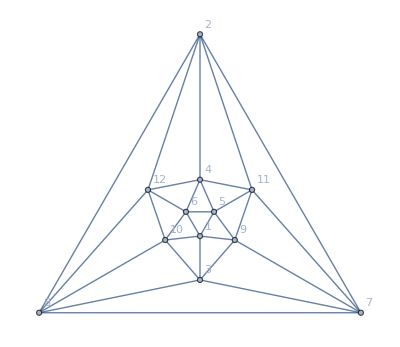

```mathematica
Graph[GraphData["IcosahedralGraph"], VertexLabels->"Name"]
```

```mathematica
VertexDegree[ReadGrof[6985]]
```

{5,5,5,5,5,5,5,5,5,5,5,5}